#### Covid analysis KZ

```mathematica
data=Import["C:\\Users\\kirill\\Desktop\\Python\\coronavirus\\covid_19_data.csv","Data"];
```

```mathematica
conf=Cases[data,k_/;k⟦4⟧=="Mainland China"]⟦;;,7⟧;
list1=Table[i,{i,1,Length@conf}];
```

```mathematica
funApp[fun_,list_]:=Normal@NonlinearModelFit[{fun,list}//Transpose,a1 x^3+b x + c,{a1,b,c},x]
```

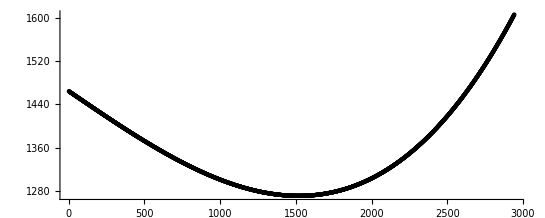

```mathematica
Graphics[{Point[{list1,Table[funApp[conf,list1]/.x->list1⟦k⟧,{k,1,Length@list1}]}//Transpose]},Axes->True]
```

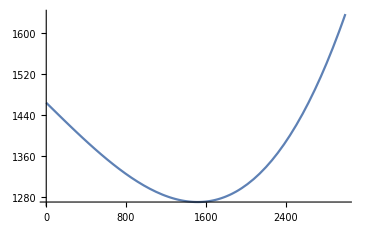

```mathematica
Plot[a/.x->k,{k,1,3000}]
```

```mathematica
leg[1]=1;
leg[2]=x;
leg[n_]:=(((2n+1)x)/(n+1)leg[n-1]-n/(n+1)leg[n-2])/√((2n+1)/2)
```

```mathematica
aCoefficient2[fun_,n_]:=Sum[fun⟦i⟧*(leg[n]/.x->list1⟦i⟧//N),{i,1,n}]
```

```mathematica
aCoefficient2[conf,20]
```

-0.0000267085

```mathematica
approximant2[fun_,n_]:=Sum[leg[k]*aCoefficient2[fun,k],{k,1,n}]
```

```mathematica
pol2=approximant2[conf,15]//Expand
```

-0.0000167727-4.6488×10^-6 x+0.000560657 x^2+0.0000566717 x^3-0.00297827 x^4-0.000193141 x^5+0.005698 x^6+0.000275998 x^7-0.00489423 x^8-0.00018756 x^9+0.00196948 x^10+0.000059853 x^11-0.000332441 x^12-7.18752×10^-6 x^13+0.0000138553 x^14

```mathematica
Show[{Graphics[{Point[{list1,conf}//Transpose]}],Plot[pol2/.x->k,{k,-20,20}]},Axes->True,PlotRange->{{-1,1},{0,10}}]
```

-Graphics-

```mathematica
interSplineL[x_,f_]:=Module[{h=Table[x⟦i⟧-x⟦i-1⟧,{i,2,Length@x}]},Table[(x⟦i+1⟧-v)/h⟦i⟧f⟦i⟧+(v-x⟦i⟧)/h⟦i⟧f⟦i+1⟧,{i,1,Length@x-1}]//FullSimplify]
```

```mathematica
visualization[pol_,point_]:=Show[{Table[Plot[pol⟦i⟧/.v->k,{k,point⟦i,1⟧,point⟦i+1,1⟧}],{i,1,Length@pol}],Graphics[{PointSize[0.015],Red,Point[point]}]},PlotRange->Full]
```

```mathematica
pol3=interSplineL[list1,conf];
```

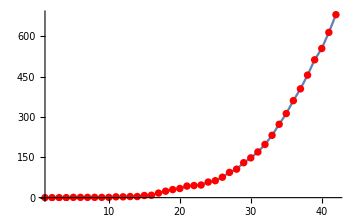

```mathematica
visualization[pol3,{list1,conf}//Transpose]
```

```mathematica
point={list1,conf}//Transpose;
```

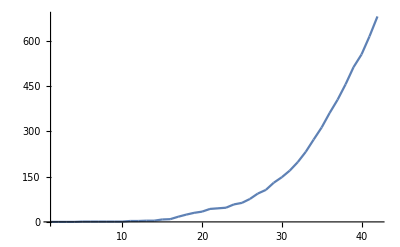

```mathematica
Show[{Table[Plot[pol3⟦i⟧/.v->k,{k,point⟦i,1⟧,point⟦i+1,1⟧}],{i,1,Length@pol3}]},PlotRange->Full]
```